```mathematica
boatDens = 1.225*(1.875/2)+710*(.125/2) ;(*Boat density (kg/m^3)*)
deckDens = 710* 0.003175 ;(*Deck area density (kg/m^2*)
mCargo = .8; (*Cargo mass (kg)*)
mMast = (π*(3/8*1/2)^2*19.685*(2.7/0.0610237))/1000; (*Mass of mast (kg)*)
comMast = {0,0,.3}; (*COM of mast (m)*)
comCargo = {0,0,.027}; 
a=.75;(*Curviness of dat boat*)
b=.12;(*height of boat (m)*)
c=.25;(*xLen/2 of boat (m)*)
(*COM of cargo (m)*)
```

```mathematica
Clear[boat,mass,com,submerged,submass,water,cob,arm]
boatFunc[n_?NumberQ,d_?NumberQ,xLen_?NumberQ,xVal_,zVal_]:=2*Abs[y/n]^1.5+d*(xVal^2/xLen^2)≤zVal≤d
boat= ImplicitRegion[boatFunc[a,b,c,x,z] ,{x,y,z}];
mass :=mass= boatDens*N[RegionMeasure[boat]]
massTot:=mass+mCargo+mMast+deckDens*RegionMeasure[ImplicitRegion[boatFunc[a,b,c,x,.1],{x,y}]]
com:=com=(N[RegionCentroid[boat]]*mass+mCargo*comCargo+mMast*comMast)/massTot
submerged[d_,t_]:=boatFunc[a,b,c,x,z]&&If[t<90,z<N[Tan[t Degree]]*y+d,z>N[Tan[t Degree]]*y+d]
submass[d_,t_]:=submass[d,t]=1000*N[RegionMeasure[ImplicitRegion[submerged[d,t],{x,y,z}]]]
water[t_]:=water[t]=FindRoot[submass[d,t]==massTot,{d,-20,20}]
cob[t_]:=cob[t]=N[RegionCentroid[ImplicitRegion[submerged[d,t]/.water[t],{x,y,z}]]]
arm[t_?NumberQ]:=Cross[cob[t]-com,{0,-Sin[t Degree]*9.81submass[d,0]/.water[0],Cos[t Degree]*9.81submass[d,0]/.water[0]}][[1]]
```

```mathematica
arm[120]
```

ImplicitRegion::msgs: Evaluation of {submerged[d,120]/.water[120],True} generated message(s) {RegionMeasure::nmet}.

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[3.0792 Abs[y]^1.5+1.92 x^2≤z≤0.12&&z<0.+d,{x,y,z}].

General::stop: Further output of RegionMeasure::nmet will be suppressed during this calculation.

0.129486

```mathematica
arm[140]
```

ImplicitRegion::msgs: Evaluation of {submerged[d,140]/.water[140],True} generated message(s) {RegionMeasure::nmet}.

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[3.0792 Abs[y]^1.5+1.92 x^2≤z≤0.12&&z<0.+d,{x,y,z}].

-0.0940399

```mathematica
RegionPlot3D[boatFunc[.75,.1,.25,x,z],{x,-.249,.249},{y,-.1,.1},{z,0,.15},AxesLabel->Automatic,BoxRatios->Automatic]
```

-Graphics3D-

ImplicitRegion::msgs: Evaluation of {submerged[d,125]/.water[125],True} generated message(s) {RegionMeasure::nmet}.

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[3.0792 Abs[y]^1.5+1.6 x^2≤z≤0.1&&z<0.+d,{x,y,z}].

ImplicitRegion::msgs: Evaluation of {submerged[d,130]/.water[130],True} generated message(s) {RegionMeasure::nmet}.

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[3.0792 Abs[y]^1.5+1.6 x^2≤z≤0.1&&z<0.+d,{x,y,z}].

ImplicitRegion::msgs: Evaluation of {submerged[d,135]/.water[135],True} generated message(s) {RegionMeasure::nmet}.

General::stop: Further output of ImplicitRegion::msgs will be suppressed during this calculation.

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[3.0792 Abs[y]^1.5+1.6 x^2≤z≤0.1&&z<0.+d,{x,y,z}].

General::stop: Further output of RegionMeasure::nmet will be suppressed during this calculation.

{0.0467876,0.00878799,-0.0284089,-0.0640583,-0.0972631}

{120,125,130,135,140}

{{120,0.0467876},{125,0.00878799},{130,-0.0284089},{135,-0.0640583},{140,-0.0972631}}

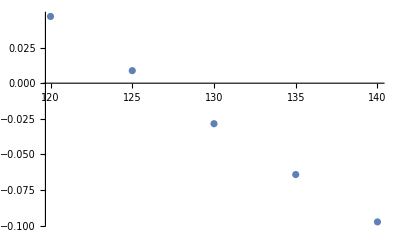

```mathematica
points = Map[arm,Range[120,140,5]]
angles = Range[120,140,5]
newPoints = Transpose[{angles,points}]
ListPlot[newPoints]
```

```mathematica
ClearAll[sliceBoat]
prisCoeff:=RegionMeasure[ImplicitRegion[submerged[d,0]/.water[0],{x,y,z}]]/(RegionMeasure[ImplicitRegion[boatFunc[.75,.1,.25,0,z],{y,z}]]*2RegionBounds[ImplicitRegion[submerged[d,0]/.water[0],{x,y,z}]][[1,2]])
```

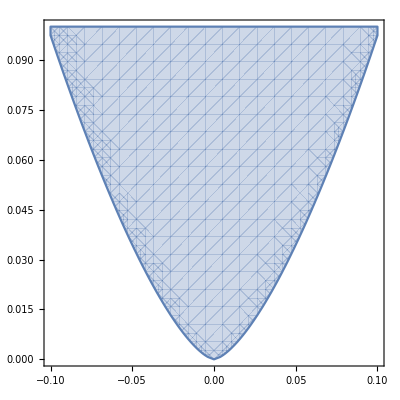

```mathematica
RegionPlot[boatFunc[.75,.1,.25,0,z],{y,-.1,.1},{z,0,.1}]
```